color function

```mathematica
IndexedMap[n_,b_]:=Hue[#/n,1,b]&
```

```mathematica
color=ColorData[63]
```

ColorDataFunction[…]

```mathematica
color=IndexedMap[50,0.8];
```

rendering methods

```mathematica
WeightedFillOpacity[color_,thickness_,list_]:={EdgeForm[{color,thickness}],FaceForm[{color,Opacity[#[[1]]]}],Polygon[#[[2]]]}&/@list
WeightedFillOpacity[color_,thickness_,scale_,list_]:={EdgeForm[{color,thickness}],FaceForm[{color,Opacity[scale*#[[1]]]}],Polygon[#[[2]]]}&/@list
WeightedFillColor[color1_,thickness_,color2_,list_]:={FaceForm[color2],{EdgeForm[{color1,thickness}],Polygon@#[[2]]}&/@list}
```

```mathematica
IndexedFillOpacity[colorfunc_,thickness_,list_]:={EdgeForm[{colorfunc[#[[1]]],thickness}],FaceForm[{colorfunc[#[[1]]],Opacity[0.3]}],Polygon[#[[2]]]}&/@list
IndexedFillOpacity[colorfunc_,thickness_,opa_,list_]:={EdgeForm[{colorfunc[#[[1]]],thickness}],FaceForm[{colorfunc[#[[1]]],Opacity[opa]}],Polygon[#[[2]]]}&/@list
IndexedNoFill[colorfunc_,thickness_,list_]:={FaceForm[],{EdgeForm[{colorfunc[#[[1]]],thickness}],Polygon[#[[2]]]}&/@list}
IndexedFillColor[colorfunc_,thickness_,color_,list_]:={FaceForm[color],{EdgeForm[{colorfunc[#[[1]]],thickness}],Polygon[#[[2]]]}&/@list}
```

```mathematica
FillOpacity[color_,thickness_,list_]:={EdgeForm[{color,thickness}],FaceForm[{color,Opacity[0.3]}],Polygon@#}&/@list
NoFill[color_,thickness_,list_]:={FaceForm[],{EdgeForm[{color,thickness}],Polygon@#}&/@list}
FillColor[color1_,thickness_,color2_,list_]:={FaceForm[color2],{EdgeForm[{color1,thickness}],Polygon@#}&/@list}
```

show grid-based results

```mathematica
data=Association@Import[NotebookDirectory[]<>"test2_no_weight_IP.json"];
```

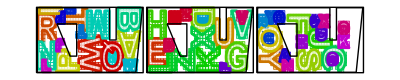

```mathematica
Graphics[{IndexedFillOpacity[color,AbsoluteThickness[0.5],0.3,data["cell"]],IndexedFillColor[color,AbsoluteThickness[2],RGBColor[1,1,1,0.7],data["shape_outer"]],IndexedNoFill[color,AbsoluteThickness[2],data["shape_inner"]],NoFill[Black,AbsoluteThickness[1],data["domain_bound"]],NoFill[Black,AbsoluteThickness[1],data["domain_outer"]],NoFill[Black,AbsoluteThickness[1],data["domain_inner"]]},ImageSize->Full,PlotRangePadding->None]
```

show post processed results

```mathematica
data=Association@Import[NotebookDirectory[]<>"mask_10_mid_IP.json"];
color=IndexedMap[52,0.8];
```

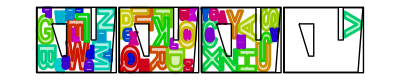

```mathematica
Graphics[{IndexedFillOpacity[color,AbsoluteThickness[2],data["shape_outer"]],IndexedNoFill[color,AbsoluteThickness[2],data["shape_inner"]],NoFill[Black,AbsoluteThickness[1],data["domain_bound"]],NoFill[Black,AbsoluteThickness[1],data["domain_outer"]],NoFill[Black,AbsoluteThickness[1],data["domain_inner"]]},ImageSize->Full,PlotRangePadding->None]
```

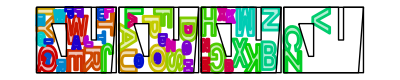

```mathematica
Graphics[{IndexedFillOpacity[color,AbsoluteThickness[2],data["postprocess_outer"]],IndexedNoFill[color,AbsoluteThickness[2],data["postprocess_inner"]],NoFill[Black,AbsoluteThickness[1],data["domain_bound"]],NoFill[Black,AbsoluteThickness[1],data["domain_outer"]],NoFill[Black,AbsoluteThickness[1],data["domain_inner"]]},ImageSize->Full,PlotRangePadding->None]
```

```mathematica
data=Association@Import[NotebookDirectory[]<>"template.json"];
```

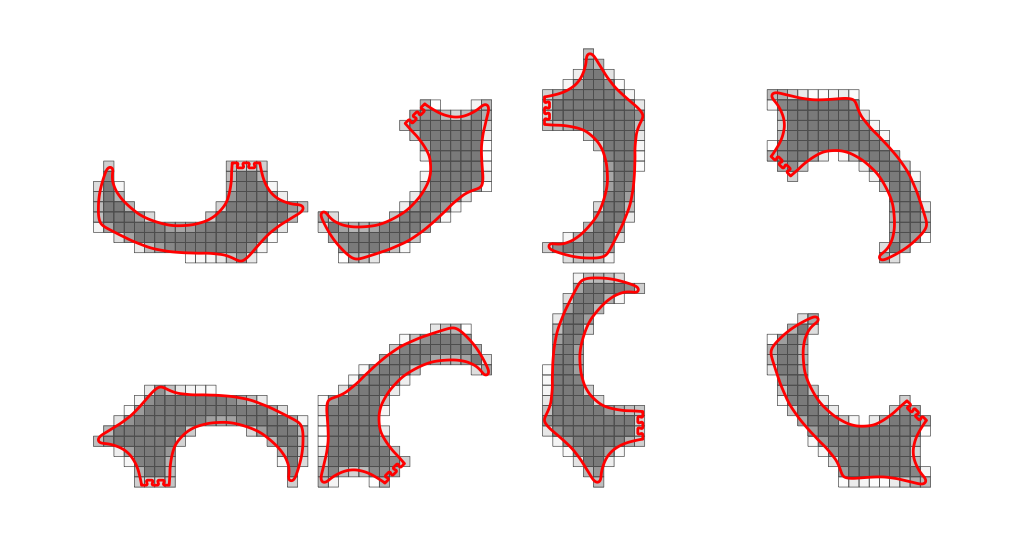

```mathematica
Graphics[{WeightedFillOpacity[GrayLevel[0.3],AbsoluteThickness[0.5],0.75,data["cell"]],NoFill[Red,AbsoluteThickness[2],data["shape_outer"]],NoFill[Red,AbsoluteThickness[2],data["shape_inner"]]},ImageSize->1024,PlotRangePadding->None]
```

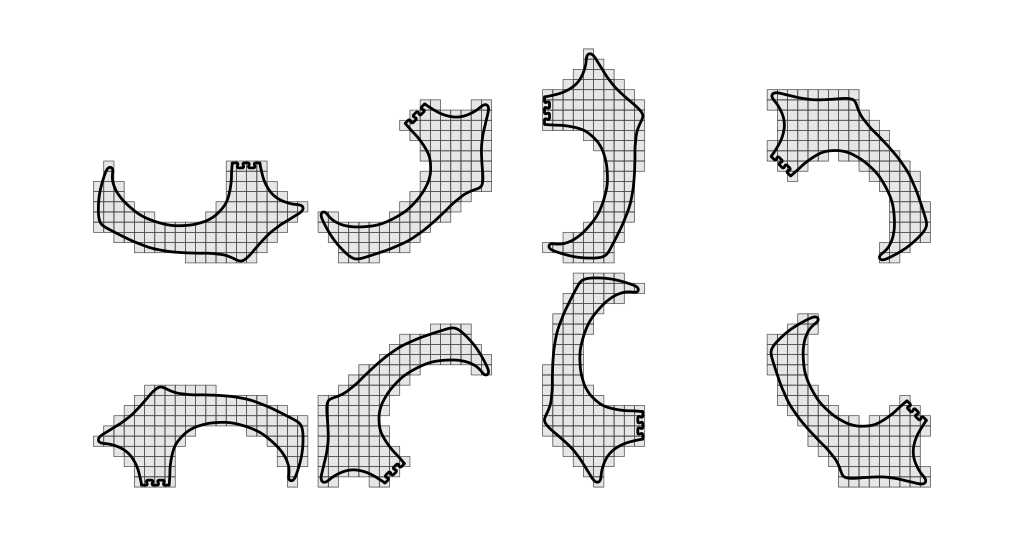

```mathematica
Graphics[{WeightedFillColor[GrayLevel[0.3],AbsoluteThickness[0.5],GrayLevel@0.9,data["cell"]],NoFill[Black,AbsoluteThickness[2],data["shape_outer"]],NoFill[Black,AbsoluteThickness[2],data["shape_inner"]]},ImageSize->1024,PlotRangePadding->None]
```